1

1

0.75

1

1

0.5

1

1

{{P[t]→InterpolatingFunction[…][t],Q[t]→InterpolatingFunction[…][t]}}

{{0,0},{0,0.75},{1,0},{0.5,0.5}}

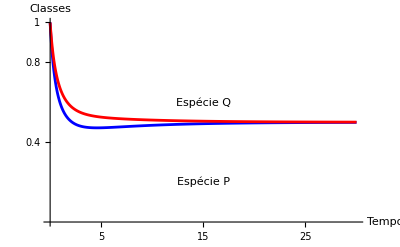

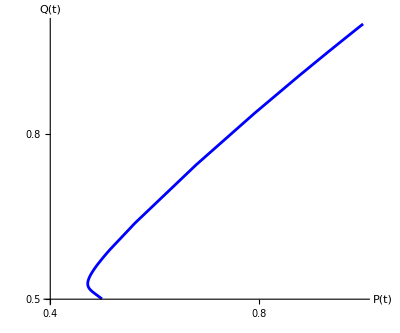

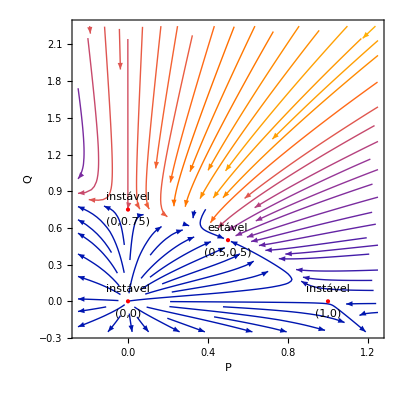

```mathematica
a=1
b=1
c=0.75
d=1
k=1
l=0.5
pini=1
qini=1


SolucaoNumerica=NDSolve[{P'[t]==(a-b*P[t]-k*Q[t])*P[t],Q'[t]==(c-d*Q[t]-l*P[t])*Q[t],P[0]==pini,Q[0]==qini},{P[t],Q[t]},{t,0,30}]


EqPontos={{0,0},{0,c/d},{a/b,0},{(c*k-a*d)/(k*l-b*d),(a*l-b*c)/(k*l-b*d)}}



PL1=Plot[Evaluate[{P[t],Q[t]}/.SolucaoNumerica],{t,0,30},PlotRange->{0,1},PlotStyle->{{Blue,Thickness[0.005]},{Red,Thickness[0.005]},{DarkerGreen,Thickness[0.005]}},Ticks->{{5,10,15,20,25,30},{0.4,0.8,1,1.6,2.0}},AxesLabel->{Tempo,Classes},LabelStyle->{Medium,Black,Bold},Epilog->{Text["StyleBox[\"Espécie Q\", \"Text\",FontColor->RGBColor[1, 0, 0]]",{15,0.6}],Text["StyleBox[\"Espécie\", \"Text\",FontColor->RGBColor[0., 0., 1.]]StyleBox[\" \", \"Text\",FontColor->RGBColor[0., 0., 1.]]StyleBox[\"P\", \"Text\",FontColor->RGBColor[0., 0., 1.]]",{15,0.2}]} ]


PL2=ParametricPlot[Evaluate[{P[t],Q[t]}/.SolucaoNumerica],{t,0,30},PlotRange->{{0.4,1},{0.5,1}},PlotStyle->{{Blue,Thickness[0.005]},{Red,Thickness[0.005]},{DarkerGreen,Thickness[0.005]}},Ticks->{{0,0.2,0.4,0.6,0.8,1},{0.5,0.6,0.8,1,1.2,1.4,1.6,1.8,2}},AxesLabel->{"P(t)","Q(t)"},LabelStyle->{Medium,Black,Bold} ]


StreamPlot[{(a-b*P-k*Q)*P,(c-d*Q-l*P)*Q},{P,-0.25,1.25},{Q,-0.25,2.25},FrameLabel->{P,Q}, StreamScale->1,StreamStyle->{Arrowheads[Small],RGBColor[0,0,1]},
Epilog->{{PointSize[Large],Red,Point[EqPontos]},Text["(0,0)",{0,-0.1}],Text["(0,0.75)",{0,-0.1+c/d}],Text["(1,0)",{0+a/b,-0.1}],Text["(0.5,0.5)",{0+(c*k-a*d)/(k*l-b*d),-0.1+(a*l-b*c)/(k*l-b*d)}],Text["instável",{0,0.1+c/d}],Text["instável",{0+a/b,0.1}],Text["instável",{0,0.1}],Text["estável",{0+(c*k-a*d)/(k*l-b*d),0.1+(a*l-b*c)/(k*l-b*d)}]}]
```